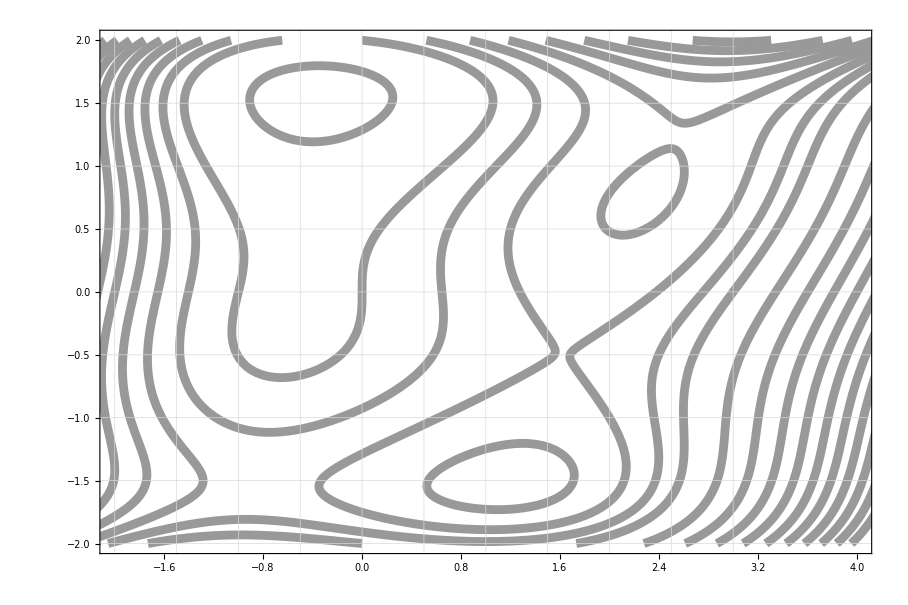

```mathematica
F[x_,y_]=2(y^3(y-2)(y+2)-x(x+1)(x-3)+x^2y);

ContourPlot[F[x,y], {x, -5, 5}, {y, -2, 2}, Contours->Join[Table[i,{i,0,100,5}],Table[i,{i,-100,0,10}]],ContourShading -> None,  AspectRatio -> 2/3,PlotRange->{{-2,4},{-2,2}},TicksStyle -> Large,
  ContourStyle -> {{Thickness[.007], GrayLevel[.6]}}, 
  PlotPoints -> 100, 
GridLines -> {Table[i, {i, xmin, xmax, .5}], 
    Table[i, {i, ymin, ymax, .5}]},
  GridLinesStyle -> {{Black, Dashed, Thickness[.001]}, {Black, Dashed,
      Thickness[.001]}}]
```

```mathematica
.
```